# Solución y simulación del modelo de única aplicación de pesticida

## Solución de la derivada

Para la solución del modelo ampliado, se aplica la ecuación de la señal de control por re-alimentación de estado u[t]=k*x[t]
Con esta solución de u[t]el modelo ampliado de Chacón toma la forma de una Ecuación Diferencial de Riccati.

Modelo ampliado:
dx[t]/dt=a×x[t]+b-k×x[t]^2
Forma de la ED de Riccati
dy[x]/dx=A[x]×y[x]^2+B[x]×y[x]+C[x]
Para solucionar la ED de Riccati, se puede tomar una solución particular de x'[t]= 0, que en este caso se denominaran y_(1,2) que corresponden a x_(1,2). Y partir de la solución particular se generaliza una solución de x'[t] donde:
x[t]=x_1+1/v[t]

Solución de la función V(t) para solución de x’[t] como ED de Riccati dy/dx=Ax^2+Bx+C

```mathematica
v=k/(a-2 y1 k)+Ce*Exp[2 y1 k (t-T)*UnitStep[t-T]-a*t]
```

Ce ⅇ^(-a t+2 k (t-T) y1 UnitStep[t-T])+k/(a-2 k y1)

```mathematica
sol=Solve[y==y1+(v^-1),Ce]
```

{{Ce→(ⅇ^(a t-2 k (t-T) y1 UnitStep[t-T]) (-a+k y+k y1))/((y-y1) (-a+2 k y1))}}

```mathematica
ce=Ce/.sol[[1]]
```

(ⅇ^(a t-2 k (t-T) y1 UnitStep[t-T]) (-a+k y+k y1))/((y-y1) (-a+2 k y1))

### Definición de soluciones y1(equivalente a x1), y2(equivalente a x2)

```mathematica
x1=(a-Sqrt[a^2 + (4 k b)])/(2k)
```

(a-√(a^2+4 b k))/(2 k)

```mathematica
x2=(a+Sqrt[a^2 + (4 k b)])/(2k)
```

(a+√(a^2+4 b k))/(2 k)

### Despeje de la constante C1

#### Evaluado en T, usando y1 (a-...)

```mathematica
cT1=ce/.{t->T,y->xT,y1->x1}//FullSimplify
```

(ⅇ^(a T) k (a+√(a^2+4 b k)-2 k xT))/(√(a^2+4 b k) (-a+√(a^2+4 b k)+2 k xT))

```mathematica
X1=y1+1/v /.{Ce->cT1,y1->x1}//FullSimplify
```

1/2 (a/k+√(a^2+4 b k) (-1/k+2/(k+(ⅇ^(-((t-T) (a+(-a+√(a^2+4 b k)) UnitStep[t-T]))) k (a+√(a^2+4 b k)-2 k xT))/(-a+√(a^2+4 b k)+2 k xT))))

#### Evaluando en T, usando y2 (a+...)

```mathematica
cT2=ce/.{t->T,y->xT,y1->x2}//FullSimplify
```

-(ⅇ^(a T) k (-a+√(a^2+4 b k)+2 k xT))/(√(a^2+4 b k) (a+√(a^2+4 b k)-2 k xT))

```mathematica
X2=y1+1/v /.{Ce->cT2,y1->x2}//FullSimplify
```

(a+√(a^2+4 b k) (1+2/(-1+(ⅇ^(-((t-T) (a-(a+√(a^2+4 b k)) UnitStep[t-T]))) (a-√(a^2+4 b k)-2 k xT))/(a+√(a^2+4 b k)-2 k xT))))/(2 k)

```mathematica
Equal[X1,X2](*Esta linea solo verifica si X1 es igual a X2*)
```

1/2 (a/k+√(a^2+4 b k) (-1/k+2/(k+(ⅇ^(-((t-T) (a+(-a+√(a^2+4 b k)) UnitStep[t-T]))) k (a+√(a^2+4 b k)-2 k xT))/(-a+√(a^2+4 b k)+2 k xT))))==(a+√(a^2+4 b k) (1+2/(-1+(ⅇ^(-((t-T) (a-(a+√(a^2+4 b k)) UnitStep[t-T]))) (a-√(a^2+4 b k)-2 k xT))/(a+√(a^2+4 b k)-2 k xT))))/(2 k)

## Gráficas - Simulación

```mathematica
pob=DSolve[{D[x[t],t]==a*x[t]+b,x[0]==x0},x[t],t]//Expand
```

{{x[t]→-b/a+(b ⅇ^(a t))/a+ⅇ^(a t) x0}}

```mathematica
(*pob1=DSolve[{D[m[t],t]==a*m[t]+b,m[0]==x0},m[t],t]//Expand*)
```

```mathematica
x[t_]=x[t]/.pob[[1]]
```

-b/a+(b ⅇ^(a t))/a+ⅇ^(a t) x0

C1 es la población inicial. Para la simulación de Chacón, la población inicial es de 35.
El coeficiente a se obtiene del valor calculado por Chacón en su tesis, para el crecimiento de trips a 21.5°C
El coeficiente b se obtiene de la simulación de Chacón para el caso de a=1.5318, donde b=0.8

```mathematica
xe[t_]=x[t]/.{x0->35,a->1.5318,b->0.8}
```

-0.522261+35.5223 ⅇ^(1.5318 t)

### Gráfica tramo antes de t=T=1.

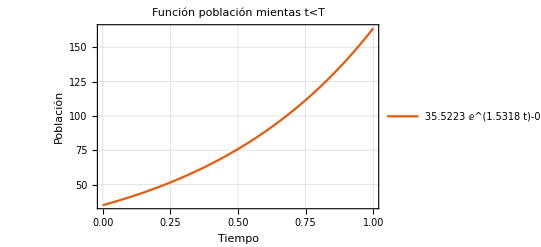

```mathematica
p1=Plot[xe[t],{t,0,1},PlotTheme->"Scientific",PlotLabel->"Función población mientas t<T",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},GridLines->Automatic(*{{0.2,0.4,0.6,0.8},{60,90,120,150}(*{xe[0.2],xe[0.4],xe[0.6],xe[0.8]}*)}*),PlotLegends->{xe[t]}]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\t menor T\\x(t)_0_1_v4.png",p1,"PNG"]*)
```

### Función después de T=1, antes de T+Δ, usando x1

```mathematica
xT=xe[1]
```

163.821

#### Definición de k a partir de linealización

La linealización a través de la matriz jacobiana (con respecto a las variables de estado) evaluada en los puntos de equilibrio da como resultado la matriz A de la representación en espacio de estado. La matriz B se obtiene a partir de la derivada parcial con respecto a la entrada. Es válido recalcar que aquí no se aplica la definición de u[t]=k*x[t]^2 para conservar la variable de control al momento de derivar.
A =-b/x_r
B =-x_r
En este caso se estableció la población de referencia x_r cómo el punto de equilibrio.
Teniendo en cuenta que los auto-valores nuevos λ_N se obtienen cómo:
A-B×k=λ_N
k=(A-λ_N)/B

```mathematica
k=(-b-λ xr)/(xr^2)
```

(-b-xr λ)/xr^2

El valor de lambda en el sistema antes de t=1 es a, o sea inestable.
Se propone que lambda para t>1 sea -a. 
Y el valor de la población de referencia x_r se establece en x_r=0.7 x_T

Se debe verificar que el valor de lambda sea mayor a b/xr

```mathematica
b/xr /.{b->0.8,xr->(0.7*xT)}
```

0.00697624

```mathematica
a>b/xr/.{b->0.8,a->1.5318,xr->(0.7*xT)}
```

True

Y se reemplazan los valores

```mathematica
k=k/.{b->0.8,λ->-a,xr->(0.7*xT)}//Simplify
```

-0.0000608349+0.0087203 a

```mathematica
k=k/.a->1.5318
```

0.0132969

```mathematica
0.7*xT
```

114.675

```mathematica
x1/.{a->1.5318,b->0.8}
```

-0.519915

```mathematica
x2/.{a->1.5318,b->0.8}
```

115.72

#### Tiempo de asentamiento esperado

```mathematica
ts=4/a/.{a->1.5318}
```

2.61131

#### Usando x1.

```mathematica
X1e[t_]=X1/.{a->1.5318,b->0.8,T->1}//Simplify
```

-0.519915+1.54563/(0.0132969-0.00389194 ⅇ^(-0.0138265 (-1.+t) (110.787+1. UnitStep[-1.+t])))

#### Función de entrada u(t)

```mathematica
u1[t_]=k* X1e[t]//Simplify
```

-0.00691327+0.0205521/(0.0132969-0.00389194 ⅇ^(-0.0138265 (-1.+t) (110.787+1. UnitStep[-1.+t])))

El pulso unitario va a durar 2.6, es decir que T+Δ=3.6 ; Δ=2.6

```mathematica
(*p2=Plot[X1e[t],{t,1,1.5},PlotTheme->"Scientific",PlotLabel->"Función población a partir de x'[t] = a*x[t] + b - k*x[t]^2",AxesLabel->{"Tiempo","Población"},PlotLegends->{X1e[t]},GridLines->Automatic]*)
```

Se verifica cuanto tiempo requiere la nueva función para llegar a x_r

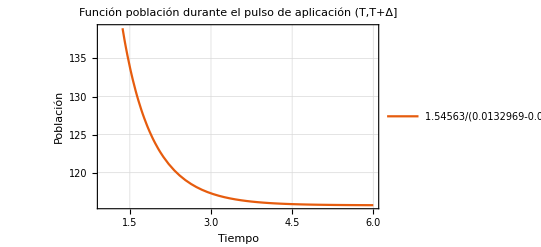

```mathematica
p2extendido=Plot[X1e[t],{t,1,6},PlotTheme->"Scientific",PlotLabel->"Función población durante el pulso de aplicación (T,T+Δ]",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X1e[t]},GridLines->Automatic]
```

Dado que la función X1e depende de una función exponencial negativa, se estabiliza asintóticamente en torno a 113 en el infinito. En este caso, convendría estimar un tiempo de asentamiento donde el margen de error sea aceptable. 
Por ejemplo: 
*Para t=4 la población ya es aproximadamente 116 individuos.
*Para t=3.5 es 116.4 individuos.
*Para t=3 es 117 individuos.
*Para t=2.5 es 119 individuos.
*Para t=2 es 123.4.
*Para t=1.5 es 133.9.
De lo que se puede concluir que a partir de 3 unidades de tiempo la población se acerca a x_r con bajo error.

#### Gráfica desde 0 hasta 3.6 usando x1.

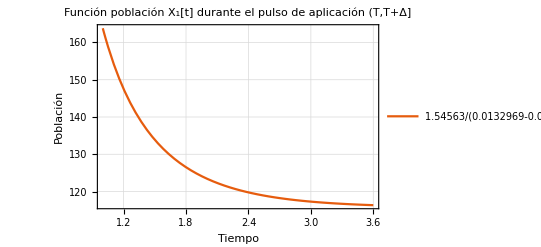

```mathematica
p2extendido2=Plot[X1e[t],{t,1,3.6},PlotTheme->"Scientific",PlotLabel->"Función población X_1[t] durante el pulso de aplicación (T,T+Δ]",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X1e[t]},GridLines->Automatic]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\fixed_UnitStep_u_kx2_usando_yparticular\\X1(t)_1_3-6.png",p2extendido2,"PNG"]*)
```

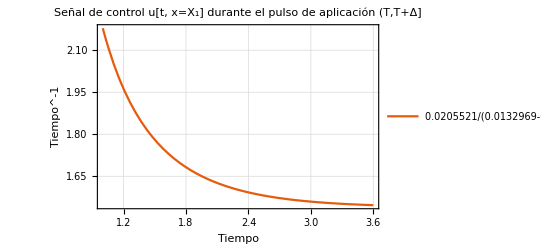

```mathematica
p2ucontrol=Plot[u1[t],{t,1,3.6},PlotTheme->"Scientific",PlotLabel->"Señal de control u[t, x=X_1] durante el pulso de aplicación (T,T+Δ]",Frame->True,FrameLabel->{{"Tiempo^-1",None},{"Tiempo",None}},PlotLegends->{u1[t]},GridLines->Automatic]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\fixed_UnitStep_u_kx2_usando_yparticular\\u1(t)_1_3-6.png",p2ucontrol,"PNG"]*)
```

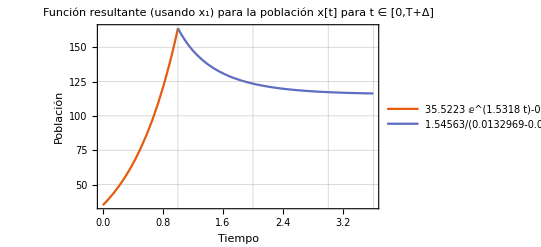

```mathematica
alternativePlot=Plot[{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)If[1<=t<=3.6,X1e[t],Undefined]   (*f2 only for t≥1*)},{t,0,3.6},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_1) para la población x[t] para t ∈ [0,T+Δ]",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X1e[t]},GridLines->{{1,2,3,3.6},{50,75,100,125,150}}]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\fixed_UnitStep_u_kx2_usando_yparticular\\x(t)_0_3-6_x1particular.png",alternativePlot,"PNG"]*)
```

### Función después de T=1, antes de T+Δ, usando x2

#### Usando x2.

```mathematica
X2e[t_]=X2/.{a->1.5318,b->0.8,T->1}//Simplify
```

115.72+116.239/(-1+3.41653 ⅇ^(3.07743 (-1.+t) (-0.497754+1. UnitStep[-1.+t])))

#### Función de entrada u(t)

```mathematica
u2[t_]=k* X2e[t]//Simplify
```

1.53871+0.452397/(-0.292695+1. ⅇ^(3.07743 (-1.+t) (-0.497754+1. UnitStep[-1.+t])))

El pulso unitario va a durar 2.6, es decir que T+Δ=3.6 ; Δ=2.6

Se verifica cuanto tiempo requiere la nueva función para llegar a x_r

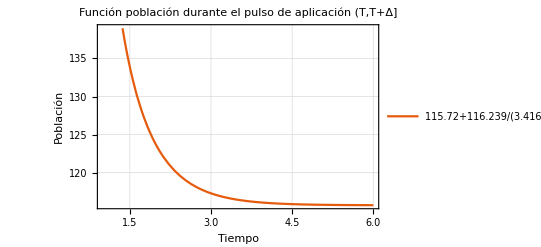

```mathematica
p3extendido=Plot[X2e[t],{t,1,6},PlotTheme->"Scientific",PlotLabel->"Función población durante el pulso de aplicación (T,T+Δ]",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X2e[t]},GridLines->Automatic]
```

#### Gráfica desde 0 hasta 3.6 usando x2.

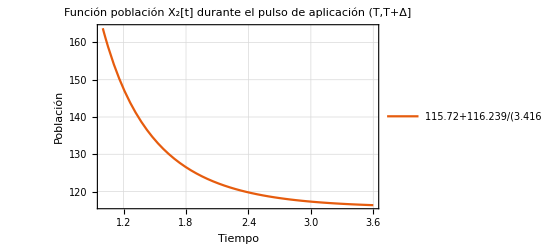

```mathematica
p3extendido2=Plot[X2e[t],{t,1,3.6},PlotTheme->"Scientific",PlotLabel->"Función población X_2[t] durante el pulso de aplicación (T,T+Δ]",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X2e[t]},GridLines->Automatic]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\fixed_UnitStep_u_kx2_usando_yparticular\\X2(t)_1_3-6.png",p3extendido2,"PNG"]*)
```

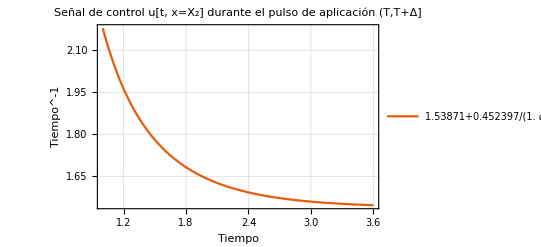

```mathematica
p3ucontrol=Plot[u2[t],{t,1,3.6},PlotTheme->"Scientific",PlotLabel->"Señal de control u[t, x=X_2] durante el pulso de aplicación (T,T+Δ]",Frame->True,FrameLabel->{{"Tiempo^-1",None},{"Tiempo",None}},PlotLegends->{u2[t]},GridLines->Automatic]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\fixed_UnitStep_u_kx2_usando_yparticular\\u2(t)_1_3-6.png",p3ucontrol,"PNG"]*)
```

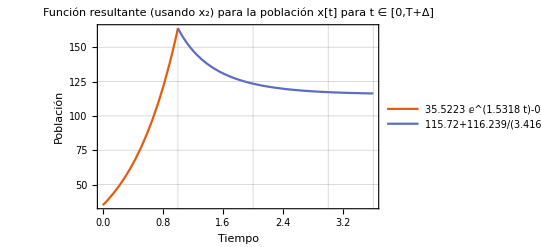

```mathematica
alternativePlot2=Plot[{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)If[1<=t<=3.6,X2e[t],Undefined]   (*f2 only for t≥1*)},{t,0,3.6},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_2) para la población x[t] para t ∈ [0,T+Δ]",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X2e[t]},GridLines->{{1,2,3,3.6},{50,75,100,125,150}}]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\fixed_UnitStep_u_kx2_usando_yparticular\\x(t)_0_3-6_x2particular.png",alternativePlot2,"PNG"]*)
```

### Función después de T+Δ, usando X1

```mathematica
X1e[3.6]
```

116.334

#### Función auxiliar V1

```mathematica
V1=C Exp[-P2 *t-(2 y1 (-K Δ))]-(P1/(P2+2 y1 P1))
```

C ⅇ^(-P2 t+2 K y1 Δ)-P1/(P2+2 P1 y1)

```mathematica
V1=V1/.{P1->(0),P2->a}
```

C ⅇ^(-a t+2 K y1 Δ)

```mathematica
sol2=Solve[Y==y1+(V1^-1),C]
```

{{C→-ⅇ^(a t-2 K y1 Δ)/(-Y+y1)}}

#### Definición de variables auxiliares de x1 y x2

```mathematica
x1aux=(a-Sqrt[a^2 + (4 K b)])/(2K)
```

(a-√(a^2+4 b K))/(2 K)

```mathematica
x2aux=(a+Sqrt[a^2 + (4 K b)])/(2K)
```

(a+√(a^2+4 b K))/(2 K)

#### Solución de la constante para x1

```mathematica
ce2=C/.sol2[[1]]
```

-ⅇ^(a t-2 K y1 Δ)/(-Y+y1)

```mathematica
c2Δ1=ce2/.{t->(T+Δ),Y->xTΔ,y1->x1aux}//FullSimplify
```

(2 ⅇ^(a T+√(a^2+4 b K) Δ) K)/(-a+√(a^2+4 b K)+2 K xTΔ)

#### Función X1 a partir de la cte de x1

```mathematica
X1Δ=y1+1/V1 /.{C->c2Δ1,y1->x1aux}//FullSimplify
```

(ⅇ^(-a (T+Δ)) (a (-ⅇ^(a t)+ⅇ^(a (T+Δ)))-ⅇ^(a (T+Δ)) √(a^2+4 b K)+ⅇ^(a t) (√(a^2+4 b K)+2 K xTΔ)))/(2 K)

#### Solución de la constante para x2

```mathematica
c2Δ2=ce2/.{t->(T+Δ),Y->xTΔ,y1->x2aux}//FullSimplify
```

-(2 ⅇ^(a T-√(a^2+4 b K) Δ) K)/(a+√(a^2+4 b K)-2 K xTΔ)

#### Función X2 a partir de la cte de x2

```mathematica
X2Δ=y1+1/V1 /.{C->c2Δ2,y1->x2aux}//FullSimplify
```

(ⅇ^(-a (T+Δ)) (a (-ⅇ^(a t)+ⅇ^(a (T+Δ)))+ⅇ^(a (T+Δ)) √(a^2+4 b K)-ⅇ^(a t) (√(a^2+4 b K)-2 K xTΔ)))/(2 K)

#### Simulación de X1Δ

```mathematica
X1e[3.6]
```

116.334

```mathematica
X1Δe[t_]=X1Δ/.{K->k,T->1,Δ->2.6,a->1.5318,b->0.8,xTΔ->X1e[3.6]}//Simplify
```

-0.519915+0.470692 ⅇ^(1.5318 t)

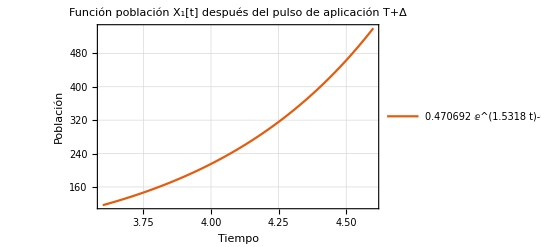

```mathematica
p4x1=Plot[X1Δe[t],{t,3.6,4.6},PlotTheme->"Scientific",PlotLabel->"Función población X_1[t] después del pulso de aplicación T+Δ",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X1Δe[t]},GridLines->Automatic]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\fixed_UnitStep_u_kx2_usando_yparticular\\X1(t)_3-6_4-6.png",p4x1,"PNG"]*)
```

#### Gráfica desde 0 hasta 4 usando x1.

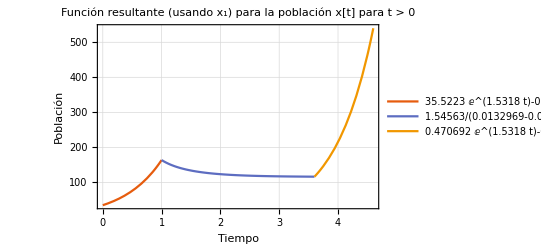

```mathematica
p5x1=Plot[
{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)
If[1<=t<=3.6,X1e[t],Undefined],   (*f2 only for 1<=t<=3.6*)
If[t>=3.6,{X1Δe[t]},Undefined]   (*f3 only for t≥3.6*)},
{t,0,4.6},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_1) para la población x[t] para t > 0",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X1e[t],X1Δe[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\fixed_UnitStep_u_kx2_usando_yparticular\\x(t)_0_4.6_x1particular.png",p5x1,"PNG"]*)
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\fixed_UnitStep_u_kx2_usando_yparticular\\x(t)_0_4.6_x1particular_v2.png",p5x1,"PNG"]*)
```

#### Simulación de X2Δ

```mathematica
X2e[3.6]
```

116.334

```mathematica
X2Δe[t_]=X2Δ/.{K->k,T->1,Δ->2.6,a->1.5318,b->0.8,xTΔ->X2e[3.6]}//Simplify
```

115.72+0.00247676 ⅇ^(1.5318 t)

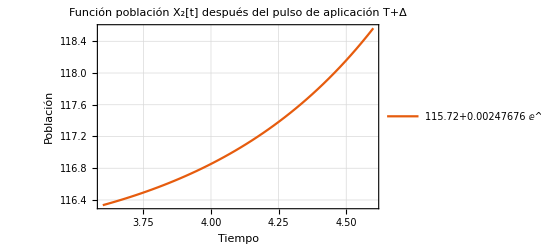

```mathematica
p4x2=Plot[X2Δe[t],{t,3.6,4.6},PlotTheme->"Scientific",PlotLabel->"Función población X_2[t] después del pulso de aplicación T+Δ",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X2Δe[t]},GridLines->Automatic]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\fixed_UnitStep_u_kx2_usando_yparticular\\X2(t)_3-6_4-6.png",p4x2,"PNG"]*)
```

#### Gráfica desde 0 hasta 4 usando x2.

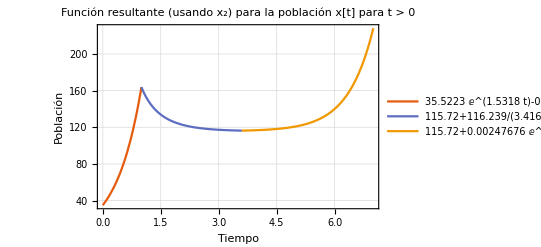

```mathematica
p5x2=Plot[
{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)
If[1<=t<=3.6,X2e[t],Undefined],   (*f2 only for 1<=t<=3.6*)
If[t>=3.6,{X2Δe[t]},Undefined]   (*f3 only for t≥3.6*)},
{t,0,7},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_2) para la población x[t] para t > 0",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X2e[t],X2Δe[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\fixed_UnitStep_u_kx2_usando_yparticular\\x(t)_0_4.6_x2particular.png",p5x2,"PNG"]*)
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\fixed_UnitStep_u_kx2_usando_yparticular\\x(t)_0_7_x2particular.png",p5x2,"PNG"]*)
```

# Solución y simulación del modelo sumatoria de aplicaciones de pesticida

## Solución de la derivada en los pulsos de aplicación

Para la solución del modelo ampliado, se aplica la ecuación de la señal de control por re-alimentación de estado u[t]=k*x[t]
Con esta solución de u[t]el modelo ampliado de Chacón toma la forma de una Ecuación Diferencial de Riccati.

Modelo ampliado:
dx[t]/dt=a×x[t]+b-k×[∑_(j=2)^m p_j[t]]×x[t]^2
Forma de la ED de Riccati
dy[x]/dx=A[x]×y[x]^2+B[x]×y[x]+C[x]
Para solucionar la ED de Riccati, se puede tomar una solución particular de x'[t]= 0, que en este caso se denominaran y_(1,2) que corresponden a x_(1,2). Y partir de la solución particular se generaliza una solución de x'[t] donde:
x[t]=x_1+1/v[t]

Solución de la función V(t) para solución de x’[t] como ED de Riccati dy/dx=Ax^2+Bx+C

```mathematica
V2=K/(a-2 Y1 K)+C2*Exp[2 Y1 K*(Δ*(j-1)+(t-Tj)*UnitStep[t-Tj])-a*t]
```

C2 ⅇ^(-a t+2 K Y1 ((-1+j) Δ+(t-Tj) UnitStep[t-Tj]))+K/(a-2 K Y1)

```mathematica
solv2=Solve[Y==Y1+(V2^-1),C2]
```

{{C2→(ⅇ^(a t-2 K Y1 ((-1+j) Δ+(t-Tj) UnitStep[t-Tj])) (-a+K Y+K Y1))/((Y-Y1) (-a+2 K Y1))}}

```mathematica
ce2=C2/.solv2[[1]]
```

(ⅇ^(a t-2 K Y1 ((-1+j) Δ+(t-Tj) UnitStep[t-Tj])) (-a+K Y+K Y1))/((Y-Y1) (-a+2 K Y1))

### Definición de soluciones y1(equivalente a x1), y2(equivalente a x2)

```mathematica
x1aux
```

(a-√(a^2+4 b K))/(2 K)

```mathematica
x2aux
```

(a+√(a^2+4 b K))/(2 K)

### Despejar C2

#### Evaluado en Tj, usando y1 (a-...)

```mathematica
ce2T1=ce2/.{t->Tj,Y->xTj,Y1->x1aux}//Simplify
```

(ⅇ^(a Tj+(-1+j) (-a+√(a^2+4 b K)) Δ) K (a+√(a^2+4 b K)-2 K xTj))/(√(a^2+4 b K) (-a+√(a^2+4 b K)+2 K xTj))

```mathematica
X1sum[t]=Y1+1/V2 /.{C2->ce2T1,Y1->x1aux}//FullSimplify
```

1/2 (a/K+√(a^2+4 b K) (-1/K+2/(K+(ⅇ^((t-Tj) (-a+(a-√(a^2+4 b K)) UnitStep[t-Tj])) K (a+√(a^2+4 b K)-2 K xTj))/(-a+√(a^2+4 b K)+2 K xTj))))

#### Evaluado en Tj, usando y2 (a+...)

```mathematica
ce2T2=ce2/.{t->Tj,Y->xTj,Y1->x2aux}//Simplify
```

-(ⅇ^(a Tj-(-1+j) (a+√(a^2+4 b K)) Δ) K (-a+√(a^2+4 b K)+2 K xTj))/(√(a^2+4 b K) (a+√(a^2+4 b K)-2 K xTj))

```mathematica
X2sum[t]=Y1+1/V2 /.{Y1->x2aux,C2->ce2T2}//FullSimplify
```

(a+√(a^2+4 b K) (1+2/(-1+(ⅇ^((t-Tj) (-a+(a+√(a^2+4 b K)) UnitStep[t-Tj])) (a-√(a^2+4 b K)-2 K xTj))/(a+√(a^2+4 b K)-2 K xTj))))/(2 K)

En ambas definiciones de X (X1 y X2) se puede observar que la función se vuelve independiente de j, lo que implica que durante la aplicacion no interviene la cantidad de aplicaciones anteriores.

### Definición general de la ganancia del controlador

```mathematica
kaux=(-b-λ xrj)/(xrj^2)
```

(-b-xrj λ)/xrj^2

## Solución de la después del pulso j y antes del pulso j+1

```mathematica
V3=C3*Exp[2 Y1 K*(Δ*j)-a*t]
```

C3 ⅇ^(-a t+2 j K Y1 Δ)

```mathematica
solv3=Solve[Y==Y1+(V3^-1),C3]
```

{{C3→-ⅇ^(a t-2 j K Y1 Δ)/(-Y+Y1)}}

```mathematica
ce3=C3/.solv3[[1]]
```

-ⅇ^(a t-2 j K Y1 Δ)/(-Y+Y1)

### Despejar C3

#### Evaluado en Tj, usando y1 (a-...)

```mathematica
ce3T1=ce3/.{t->TjΔ,Y->xTjΔ,Y1->x1aux}//Simplify
```

(2 ⅇ^(a TjΔ-a j Δ+j √(a^2+4 b K) Δ) K)/(-a+√(a^2+4 b K)+2 K xTjΔ)

```mathematica
X1aftersum[t]=Y1+1/V3 /.{C3->ce3T1,Y1->x1aux}//FullSimplify
```

(ⅇ^(-a TjΔ) (a (-ⅇ^(a t)+ⅇ^(a TjΔ))-ⅇ^(a TjΔ) √(a^2+4 b K)+ⅇ^(a t) (√(a^2+4 b K)+2 K xTjΔ)))/(2 K)

#### Evaluado en Tj, usando y2 (a+...)

```mathematica
ce3T2=ce3/.{t->TjΔ,Y->xTjΔ,Y1->x2aux}//Simplify
```

-(2 ⅇ^(a TjΔ-j (a+√(a^2+4 b K)) Δ) K)/(a+√(a^2+4 b K)-2 K xTjΔ)

```mathematica
X2aftersum[t]=Y1+1/V3 /.{Y1->x2aux,C3->ce3T2}//FullSimplify
```

(a+√(a^2+4 b K)-ⅇ^(a (t-TjΔ)) (a+√(a^2+4 b K)-2 K xTjΔ))/(2 K)

En ambas definiciones de X (X1 y X2) se puede observar que la función se vuelve independiente de j, lo que implica que

## Gráficas - Simulación (Misma población de referencia para todos los pulsos)

En esta sección se simula considerando el mismo x_r para todos los pulsos j, por lo que la ganancia k sigue siendo valida en esta sección.

```mathematica
k
```

0.0132969

Así mismo se toma como base el análisis realizado para el modelo de única aplicación, ya que el modelo de la sumatoria es una generalización del modelo de única aplicación.
El periodo de aplicación T_j se fija en 1+Δ, y se realizara hasta la tercera aplicación.
Nota: Más adelante se define la variable T_4 solo para indicar el final de las aplicaciones, no implica una cuarta aplicación.

```mathematica
T1=1
```

1

```mathematica
T2=T1+Δ+1
```

2+Δ

```mathematica
xTj2={X1Δe[T2/.{Δ->2.6}],X2Δe[T2/.{Δ->2.6}]}
```

{540.106,118.564}

### Segunda aplicación - Pulso de aplicación

#### Función X1

```mathematica
X1sume[t_]=X1sum[t]/.{K->k,a->1.5318,b->0.8,Tj->T2,xTj->xTj2[[1]]}/.Δ->2.6//FullSimplify
```

-0.519915+1/(0.00860293-0.00675322 ⅇ^((-4.6+t) (-1.5318-0.0138265 UnitStep[-4.6+t])))

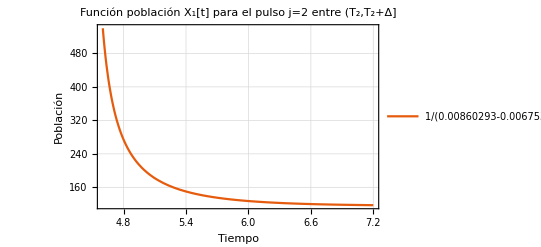

```mathematica
psum1=Plot[X1sume[t],{t,4.6,4.6+2.6},PlotTheme->"Scientific",PlotLabel->"Función población X_1[t] para el pulso j=2 entre (T_2,T_2+Δ]",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X1sume[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j2\\x(t)_j2_4-6_7-2_x1particular.png",psum1,"PNG"]*)
```

#### Señal de control u para X1

```mathematica
uX1sum[t_]=k* X1sume[t]//FullSimplify
```

0.0132969 (-0.519915+1/(0.00860293-0.00675322 ⅇ^((-4.6+t) (-1.5318-0.0138265 UnitStep[-4.6+t]))))

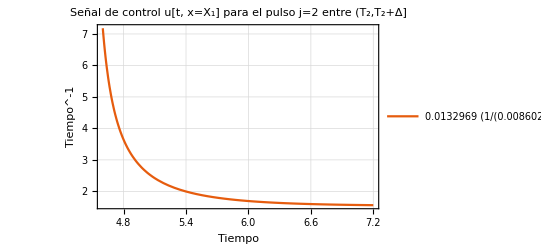

```mathematica
psum2=Plot[uX1sum[t],{t,4.6,4.6+2.6},PlotTheme->"Scientific",PlotLabel->"Señal de control u[t, x=X_1] para el pulso j=2 entre (T_2,T_2+Δ]",Frame->True,FrameLabel->{{"Tiempo^-1",None},{"Tiempo",None}},PlotLegends->{uX1sum[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j2\\u(t)_j2_4-6_7-2_x1particular.png",psum2,"PNG"]*)
```

#### Función X, usando X1, en el rango [0,T2+Δ]

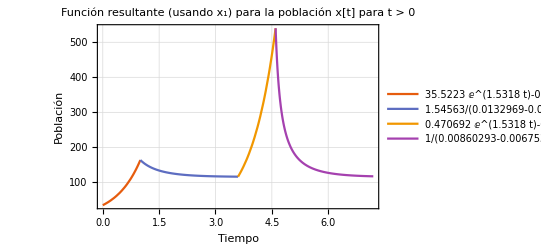

```mathematica
P1sumx1=Plot[
{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)
If[1<=t<=3.6,X1e[t],Undefined],   (*f2 only for 1<=t<=3.6*)
If[3.6<=t<=4.6,X1Δe[t],Undefined],
If[t>=4.6,X1sume[t],Undefined]   (*f3 only for t≥3.6*)},
{t,0,(T2+Δ)/.Δ->2.6},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_1) para la población x[t] para t > 0",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X1e[t],X1Δe[t],X1sume[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j2\\x(t)_j2_0_7-2_x1particular.png",P1sumx1,"PNG"]*)
```

#### Función X2

```mathematica
X2sume[t_]=X2sum[t]/.{K->k,a->1.5318,b->0.8,Tj->T2,xTj->xTj2[[2]]}/.Δ->2.6//FullSimplify
```

115.72+1/(-0.00860293+0.360128 ⅇ^((-4.6+t) (-1.5318+3.07743 UnitStep[-4.6+t])))

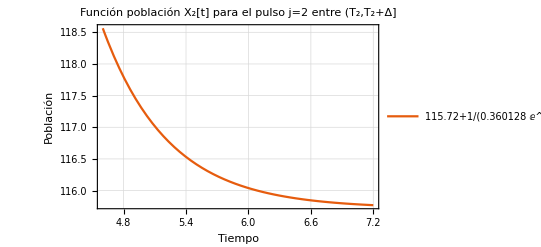

```mathematica
psum3=Plot[X2sume[t],{t,4.6,4.6+2.6},PlotTheme->"Scientific",PlotLabel->"Función población X_2[t] para el pulso j=2 entre (T_2,T_2+Δ]",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X2sume[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j2\\x(t)_j2_4-6_7-2_x2particular.png",psum3,"PNG"]*)
```

#### Señal de control u para X2

```mathematica
uX2sum[t_]=k* X2sume[t]//FullSimplify
```

0.0132969 (115.72+1/(-0.00860293+0.360128 ⅇ^((-4.6+t) (-1.5318+3.07743 UnitStep[-4.6+t]))))

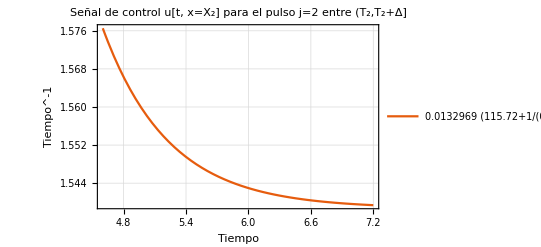

```mathematica
psum4=Plot[uX2sum[t],{t,4.6,4.6+2.6},PlotTheme->"Scientific",PlotLabel->"Señal de control u[t, x=X_2] para el pulso j=2 entre (T_2,T_2+Δ]",Frame->True,FrameLabel->{{"Tiempo^-1",None},{"Tiempo",None}},PlotLegends->{uX2sum[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j2\\u(t)_j2_4-6_7-2_x2particular.png",psum4,"PNG"]*)
```

#### Función X, usando X2, en el rango [0,T2+Δ]

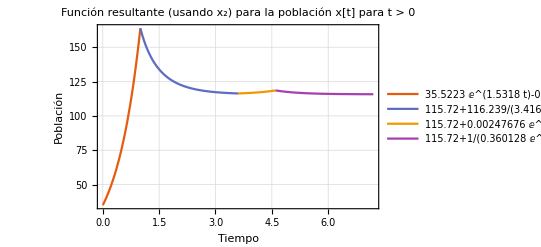

```mathematica
P2sumx2=Plot[
{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)
If[1<=t<=3.6,X2e[t],Undefined],   (*f2 only for 1<=t<=3.6*)
If[3.6<=t<=4.6,X2Δe[t],Undefined],
If[t>=4.6,X2sume[t],Undefined]   (*f3 only for t≥3.6*)},
{t,0,(T2+Δ)/.Δ->2.6},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_2) para la población x[t] para t > 0",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X2e[t],X2Δe[t],X2sume[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j2\\x(t)_j2_0_7-2_x2particular.png",P2sumx2,"PNG"]*)
```

### Segunda aplicación - Después del pulso 2 y antes del pulso 3

```mathematica
T3=T2+Δ+1
```

3+2 Δ

```mathematica
xTj2Δ={X1sume[(T2+Δ)/.{Δ->2.6}],X2sume[(T2+Δ)/.{Δ->2.6}]}
```

{117.383,115.769}

#### Función X1

```mathematica
X1aftersumj2[t_]=X1aftersum[t]/.{K->k,a->1.5318,b->0.8,TjΔ->(T2+Δ),xTjΔ->xTj2Δ[[1]]}/.Δ->2.6//Simplify
```

-0.519915+0.00191298 ⅇ^(1.5318 t)

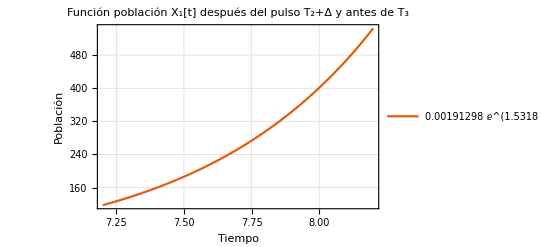

```mathematica
psum5=Plot[X1aftersumj2[t],{t,(T2+Δ),T3}/.Δ->2.6,PlotTheme->"Scientific",PlotLabel->"Función población X_1[t] después del pulso T_2+Δ y antes de T_3",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X1aftersumj2[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j2\\x(t)_j2_7-2_8-2_x1particular.png",psum5,"PNG"]*)
```

#### Función X, usando X1, en el rango [0,T3]

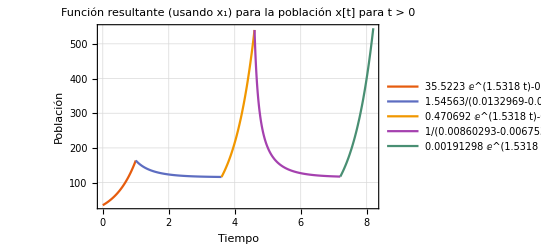

```mathematica
P3sumx1=Plot[
{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)
If[1<=t<=3.6,X1e[t],Undefined],   (*f2 only for 1<=t<=3.6*)
If[3.6<=t<=4.6,X1Δe[t],Undefined],
If[4.6<=t<=(T2+Δ)/.Δ->2.6,X1sume[t],Undefined],
If[t>=(T2+Δ)/.Δ->2.6,X1aftersumj2[t],Undefined]   (*f3 only for t≥3.6*)},
{t,0,T3/.Δ->2.6},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_1) para la población x[t] para t > 0",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X1e[t],X1Δe[t],X1sume[t],X1aftersumj2[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j2\\x(t)_j2_4-6_8-2_x1particular.png",P3sumx1,"PNG"]*)
```

#### Función X2

```mathematica
X2aftersumj2[t_]=X2aftersum[t]/.{K->k,a->1.5318,b->0.8,TjΔ->(T2+Δ),xTjΔ->xTj2Δ[[2]]}/.Δ->2.6//Simplify
```

115.72+8.10298×10^-7 ⅇ^(1.5318 t)

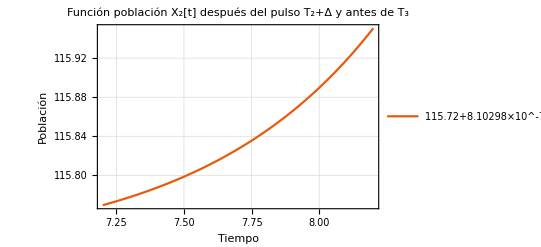

```mathematica
psum6=Plot[X2aftersumj2[t],{t,(T2+Δ),T3}/.Δ->2.6,PlotTheme->"Scientific",PlotLabel->"Función población X_2[t] después del pulso T_2+Δ y antes de T_3",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X2aftersumj2[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j2\\x(t)_j2_7-2_8-2_x2particular.png",psum6,"PNG"]*)
```

#### Función X, usando X2, en el rango [0,T3]

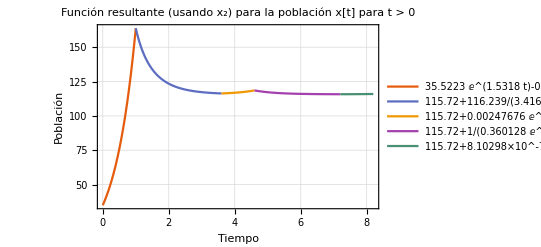

```mathematica
P4sumx2=Plot[
{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)
If[1<=t<=3.6,X2e[t],Undefined],   (*f2 only for 1<=t<=3.6*)
If[3.6<=t<=4.6,X2Δe[t],Undefined],
If[4.6<=t<=(T2+Δ)/.Δ->2.6,X2sume[t],Undefined],
If[t>=(T2+Δ)/.Δ->2.6,X2aftersumj2[t],Undefined]   (*f3 only for t≥3.6*)},
{t,0,T3/.Δ->2.6},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_2) para la población x[t] para t > 0",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X2e[t],X2Δe[t],X2sume[t],X2aftersumj2[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j2\\x(t)_j2_4-6_8-2_x2particular.png",P4sumx2,"PNG"]*)
```

### Tercera aplicación - Pulso de aplicación

```mathematica
xTj3={X1aftersumj2[(T3)/.{Δ->2.6}],X2aftersumj2[(T3)/.{Δ->2.6}]}
```

{544.959,115.951}

#### Función X1

```mathematica
X1sumj3[t_]=X1sum[t]/.{K->k,a->1.5318,b->0.8,Tj->T3,xTj->xTj3[[1]]}/.Δ->2.6//FullSimplify
```

-0.519915+1/(0.00860293-0.00676968 ⅇ^((-8.2+t) (-1.5318-0.0138265 UnitStep[-8.2+t])))

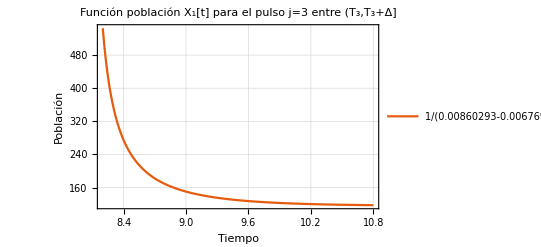

```mathematica
psum7=Plot[X1sumj3[t],{t,T3,T3+Δ}/.Δ->2.6,PlotTheme->"Scientific",PlotLabel->"Función población X_1[t] para el pulso j=3 entre (T_3,T_3+Δ]",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X1sumj3[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j3\\x(t)_j3_8-2_10-8_x1particular.png",psum7,"PNG"]*)
```

#### Señal de control u para X1

```mathematica
uX1sumj3[t_]=k* X1sumj3[t]//FullSimplify
```

0.0132969 (-0.519915+1/(0.00860293-0.00676968 ⅇ^((-8.2+t) (-1.5318-0.0138265 UnitStep[-8.2+t]))))

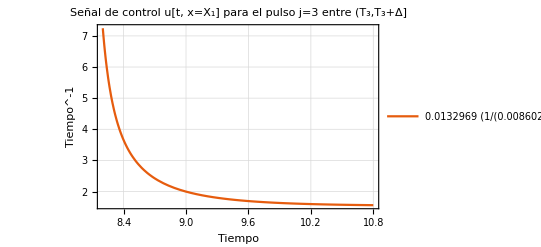

```mathematica
psum8=Plot[uX1sumj3[t],{t,T3,T3+Δ}/.Δ->2.6,PlotTheme->"Scientific",PlotLabel->"Señal de control u[t, x=X_1] para el pulso j=3 entre (T_3,T_3+Δ]",Frame->True,FrameLabel->{{"Tiempo^-1",None},{"Tiempo",None}},PlotLegends->{uX1sumj3[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j3\\u(t)_j3_8-2_10-8_x1particular.png",psum8,"PNG"]*)
```

#### Función X, usando X1, en el rango [0,T2+Δ]

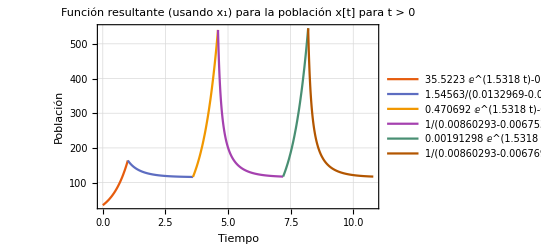

```mathematica
P5sumx1=Plot[
{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)
If[1<=t<=3.6,X1e[t],Undefined],   (*f2 only for 1<=t<=3.6*)
If[3.6<=t<=4.6,X1Δe[t],Undefined],
If[4.6<=t<=(T2+Δ)/.Δ->2.6,X1sume[t],Undefined],
If[(T2+Δ/.Δ->2.6)<=t<=(T3/.Δ->2.6),X1aftersumj2[t],Undefined],   (*f3 only for t≥3.6*)
If[t>=T3/.Δ->2.6,X1sumj3[t],Undefined]},
{t,0,(T3+Δ)/.Δ->2.6},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_1) para la población x[t] para t > 0",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X1e[t],X1Δe[t],X1sume[t],X1aftersumj2[t],X1sumj3[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j3\\x(t)_j3_0_10-8_x1particular.png",P5sumx1,"PNG"]*)
```

#### Función X2

```mathematica
X2sumj3[t_]=X2sum[t]/.{K->k,a->1.5318,b->0.8,Tj->T3,xTj->xTj3[[2]]}/.Δ->2.6//FullSimplify
```

115.72+1/(-0.00860293+4.33659 ⅇ^((-8.2+t) (-1.5318+3.07743 UnitStep[-8.2+t])))

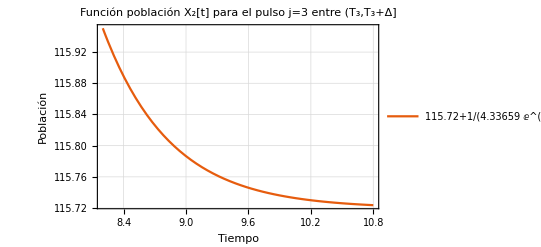

```mathematica
psum9=Plot[X2sumj3[t],{t,T3,T3+Δ}/.Δ->2.6,PlotTheme->"Scientific",PlotLabel->"Función población X_2[t] para el pulso j=3 entre (T_3,T_3+Δ]",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X2sumj3[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j3\\x(t)_j3_8-2_10-8_x2particular.png",psum9,"PNG"]*)
```

#### Señal de control u para X2

```mathematica
uX2sumj3[t_]=k* X2sumj3[t]//FullSimplify
```

0.0132969 (115.72+1/(-0.00860293+4.33659 ⅇ^((-8.2+t) (-1.5318+3.07743 UnitStep[-8.2+t]))))

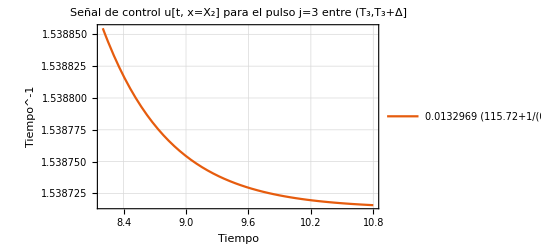

```mathematica
psum10=Plot[uX2sum[t],{t,T3,T3+Δ}/.Δ->2.6,PlotTheme->"Scientific",PlotLabel->"Señal de control u[t, x=X_2] para el pulso j=3 entre (T_3,T_3+Δ]",Frame->True,FrameLabel->{{"Tiempo^-1",None},{"Tiempo",None}},PlotLegends->{uX2sum[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j3\\u(t)_j3_8-2_10-8_x2particular.png",psum10,"PNG"]*)
```

#### Función X, usando X2, en el rango [0,T2+Δ]

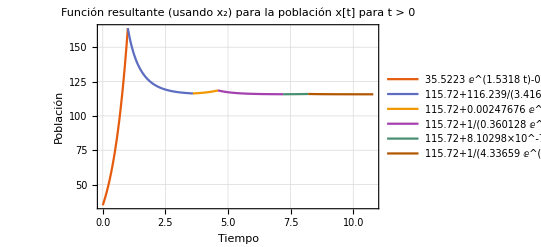

```mathematica
P6sumx2=Plot[
{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)
If[1<=t<=3.6,X2e[t],Undefined],   (*f2 only for 1<=t<=3.6*)
If[3.6<=t<=4.6,X2Δe[t],Undefined],
If[4.6<=t<=(T2+Δ)/.Δ->2.6,X2sume[t],Undefined],
If[(T2+Δ/.Δ->2.6)<=t<=(T3/.Δ->2.6),X2aftersumj2[t],Undefined],   (*f3 only for t≥3.6*)
If[t>=T3/.Δ->2.6,X2sumj3[t],Undefined]},
{t,0,(T3+Δ)/.Δ->2.6},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_2) para la población x[t] para t > 0",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X2e[t],X2Δe[t],X2sume[t],X2aftersumj2[t],X2sumj3[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j3\\x(t)_j3_0_10-8_x2particular.png",P6sumx2,"PNG"]*)
```

### Tercera aplicación - Después del pulso 3 y antes del pulso 4

```mathematica
T4=T3+Δ+1
```

4+3 Δ

```mathematica
xTj3Δ={X1sumj3[(T3+Δ)/.{Δ->2.6}],X2sumj3[(T3+Δ)/.{Δ->2.6}]}
```

{117.388,115.724}

#### Función X1

```mathematica
X1aftersumj3[t_]=X1aftersum[t]/.{K->k,a->1.5318,b->0.8,TjΔ->(T3+Δ),xTjΔ->xTj3Δ[[1]]}/.Δ->2.6//Simplify
```

-0.519915+7.70578×10^-6 ⅇ^(1.5318 t)

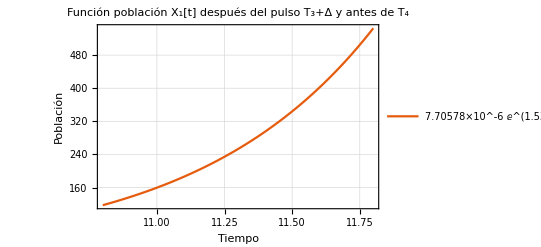

```mathematica
psum11=Plot[X1aftersumj3[t],{t,(T3+Δ),T4}/.Δ->2.6,PlotTheme->"Scientific",PlotLabel->"Función población X_1[t] después del pulso T_3+Δ y antes de T_4",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X1aftersumj3[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j3\\x(t)_j3_10-8_11-8_x1particular.png",psum11,"PNG"]*)
```

#### Función X, usando X1, en el rango [0,T4]

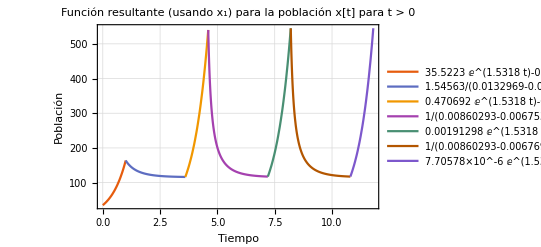

```mathematica
P7sumx1=Plot[
{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)
If[1<=t<=3.6,X1e[t],Undefined],   (*f2 only for 1<=t<=3.6*)
If[3.6<=t<=4.6,X1Δe[t],Undefined],
If[4.6<=t<=(T2+Δ)/.Δ->2.6,X1sume[t],Undefined],
If[(T2+Δ/.Δ->2.6)<=t<=(T3/.Δ->2.6),X1aftersumj2[t],Undefined],   (*f3 only for t≥3.6*)
If[(T3/.Δ->2.6)<=t<=(T3+Δ/.Δ->2.6),X1sumj3[t],Undefined],
If[t>=(T3+Δ)/.Δ->2.6,X1aftersumj3[t],Undefined]},
{t,0,T4/.Δ->2.6},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_1) para la población x[t] para t > 0",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X1e[t],X1Δe[t],X1sume[t],X1aftersumj2[t],X1sumj3[t],X1aftersumj3[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j3\\x(t)_j3_0_11-8_x1particular.png",P7sumx1,"PNG"]*)
```

#### Función X2

```mathematica
X2aftersumj3[t_]=X2aftersum[t]/.{K->k,a->1.5318,b->0.8,TjΔ->(T3+Δ),xTjΔ->xTj3Δ[[2]]}/.Δ->2.6//Simplify
```

115.72+2.7094×10^-10 ⅇ^(1.5318 t)

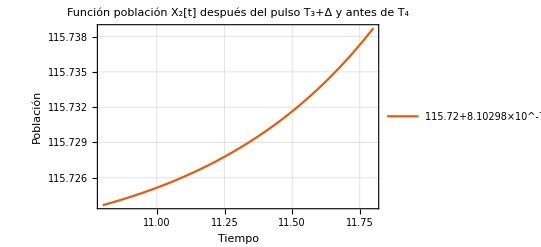

```mathematica
psum12=Plot[X2aftersumj3[t],{t,(T3+Δ),T4}/.Δ->2.6,PlotTheme->"Scientific",PlotLabel->"Función población X_2[t] después del pulso T_3+Δ y antes de T_4",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{X2aftersumj2[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j3\\x(t)_j3_10-8_11-8_x2particular.png",psum12,"PNG"]*)
```

#### Función X, usando X2, en el rango [0,T3]

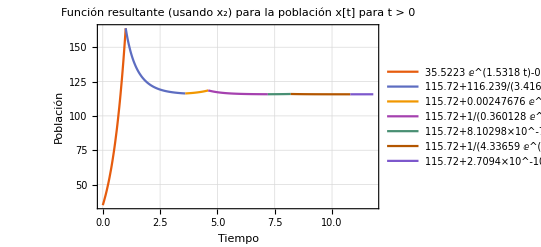

```mathematica
P8sumx2=Plot[
{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)
If[1<=t<=3.6,X2e[t],Undefined],   (*f2 only for 1<=t<=3.6*)
If[3.6<=t<=4.6,X2Δe[t],Undefined],
If[4.6<=t<=(T2+Δ)/.Δ->2.6,X2sume[t],Undefined],
If[(T2+Δ/.Δ->2.6)<=t<=(T3/.Δ->2.6),X2aftersumj2[t],Undefined],   (*f3 only for t≥3.6*)
If[(T3/.Δ->2.6)<=t<=(T3+Δ/.Δ->2.6),X2sumj3[t],Undefined],
If[t>=(T3+Δ)/.Δ->2.6,X2aftersumj3[t],Undefined]},
{t,0,T4/.Δ->2.6},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_2) para la población x[t] para t > 0",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X2e[t],X2Δe[t],X2sume[t],X2aftersumj2[t],X2sumj3[t],X2aftersumj3[t]},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j3\\x(t)_j3_0_11-8_x2particular.png",P8sumx2,"PNG"]*)
```

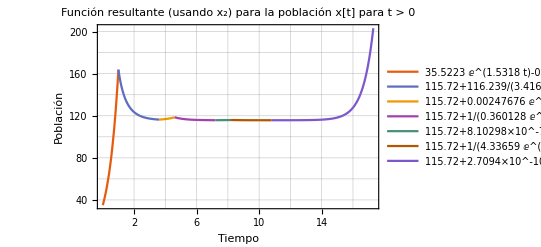

```mathematica
P9sumx2=Plot[
{If[t<=1,xe[t],Undefined],(*f1 only for t≤1*)
If[1<=t<=3.6,X2e[t],Undefined],   (*f2 only for 1<=t<=3.6*)
If[3.6<=t<=4.6,X2Δe[t],Undefined],
If[4.6<=t<=(T2+Δ)/.Δ->2.6,X2sume[t],Undefined],
If[(T2+Δ/.Δ->2.6)<=t<=(T3/.Δ->2.6),X2aftersumj2[t],Undefined],   (*f3 only for t≥3.6*)
If[(T3/.Δ->2.6)<=t<=(T3+Δ/.Δ->2.6),X2sumj3[t],Undefined],
If[t>=(T3+Δ)/.Δ->2.6,X2aftersumj3[t],Undefined]},
{t,0,(T4+5.5/.Δ->2.6)},PlotTheme->"Scientific",PlotLabel->"Función resultante (usando x_2) para la población x[t] para t > 0",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLegends->{xe[t],X2e[t],X2Δe[t],X2sume[t],X2aftersumj2[t],X2sumj3[t],X2aftersumj3[t]},FrameTicks->{{{40,60,80,100,120,140,160,180,200,220}, None}, {{2,4,6,8,10,12,14,16,18}, None}},GridLines->{{2,4,6,8,10,12,14,16,18},{40,60,80,100,120,140,160,180,200,220}},PlotRange->All]
```

```mathematica
(*Export["D:\\Documentos\\UNIVERSIDAD\\z.PROYECTO DE GRADO\\Figuras\\Sumatoria_UnitStep_u_kx2_usando_yparticular\\j3\\x(t)_j3_0_17-3_x2particular.png",P9sumx2,"PNG"]*)
```